# Smooth code for ORT

```mathematica
eta3 here represents etaxy
```

eta3 etaxy here represents

```mathematica
Clear["Global`*"]
```

```mathematica
param={v01->1.5,v02->2,v11->2,v12->2.5,v21->1.8,v22->2.2,eta11->0,eta12->0,eta21->0,eta22->0,eta31->0,eta32->0,alfa->4,dz->2,th1->0,th2->Pi/6}
```

{v01→1.5,v02→2,v11→2,v12→2.5,v21→1.8,v22→2.2,eta11→0,eta12→0,eta21→0,eta22→0,eta31→0,eta32→0,alfa→4,dz→2,th1→0,th2→π/6}

```mathematica
z0=3
```

3

```mathematica
delta11=((v11/v01)^2-1)/2;
delta12=((v12/v02)^2-1)/2;
delta21=((v21/v01)^2-1)/2;
delta22=((v22/v02)^2-1)/2;
```

```mathematica
epslion11=((1+2*delta11)*(1+2*eta11)-1)/2;
epslion12=((1+2*delta12)*(1+2*eta12)-1)/2;
epslion21=((1+2*delta21)*(1+2*eta21)-1)/2;
epslion22=((1+2*delta22)*(1+2*eta22)-1)/2;
```

#### delta3 from Vasconcelos and Tsvankin (2006)

```mathematica
delta31=(-2 eta11-2 eta21-4 eta11 eta21-2 epslion11 (1+2 eta11) (1+2 eta21)+2 eta31+eta31^2+2 epslion21 (1+eta31)^2)/(2 (1+2 epslion11) (1+2 eta11) (1+2 eta21));
delta32=(-2 eta12-2 eta22-4 eta12 eta22-2 epslion12 (1+2 eta12) (1+2 eta22)+2 eta32+eta32^2+2 epslion22 (1+eta32)^2)/(2 (1+2 epslion12) (1+2 eta12) (1+2 eta22));
```

## n1 smoothing

## unsmoothed model

```mathematica
a=1/v01/.param;
```

```mathematica
b=1/v02/.param;
```

```mathematica
K=Piecewise[{{a,x<z0},{b,x≥z0}}]
```

Piecewise[{{0.666667, x<3}, {1/2, x≥3}, {0, True}}]

```mathematica
m1:=a/;x<z0;
```

```mathematica
m1:=b/;x≥z0;
```

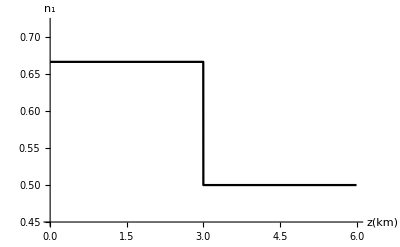

```mathematica
L1=Plot[m1,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0.45},PlotRange->{{0,6},{0.45,0.72}},AxesLabel->{Style["z(km)",FontSize->15],Style["n_1",FontSize->15]}]
```

```mathematica
FF=K*E^(2*(x-z0)^2)/.param;
```

```mathematica
n1=(Integrate[FF,{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

## delta1 smoothing

```mathematica
a1=delta11/.param;
```

```mathematica
b1=delta12/.param;
```

```mathematica
K1=Piecewise[{{a1,x<z0},{b1,x≥z0}}]
```

Piecewise[{{0.388889, x<3}, {0.28125, x≥3}, {0, True}}]

## unsmooth model for V1

```mathematica
m2:=a1/;x<z0;
```

```mathematica
m2:=b1/;x≥z0;
```

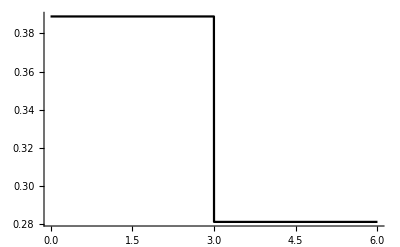

```mathematica
L11=Plot[m2,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
DELTA1=(Integrate[K1*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

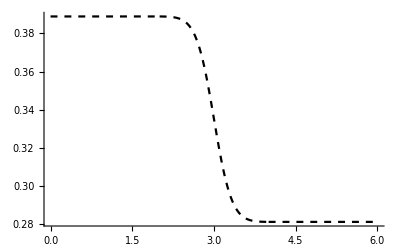

```mathematica
L12=Plot[DELTA1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All]
```

## delta2 smoothing

## smoothed model

```mathematica
a2=delta21/.param;
```

```mathematica
b2=delta22/.param;
```

```mathematica
K2=Piecewise[{{a2,x<z0},{b2,x≥z0}}]
```

Piecewise[{{0.22, x<3}, {0.105, x≥3}, {0, True}}]

## unsmooth model for V2

```mathematica
m3:=a2/;x<z0;
```

```mathematica
m3:=b2/;x≥z0;
```

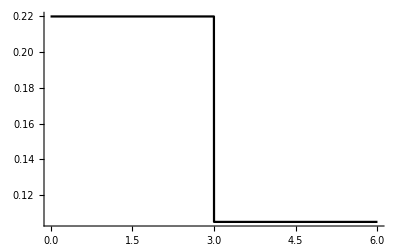

```mathematica
L21=Plot[m3,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
DELTA2=(Integrate[K2*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

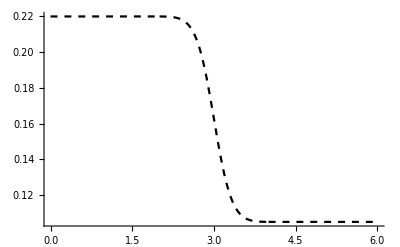

```mathematica
L22=Plot[DELTA2,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All]
```

## epslion1 smoothing

## composite param

```mathematica
a3=epslion11/.param;
```

```mathematica
b3=epslion12/.param;
```

```mathematica
K3=Piecewise[{{a3,x<z0},{b3,x≥z0}}]
```

Piecewise[{{0.388889, x<3}, {0.28125, x≥3}, {0, True}}]

```mathematica
m4:=a3/;x<z0;
```

```mathematica
m4:=b3/;x≥z0;
```

```mathematica
Le1=Plot[m4,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
EPSLION1=(Integrate[K3*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
Le2=Plot[EPSLION1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All]
```

-Graphics-

## epslion2 smoothing

## composite param

```mathematica
a4=epslion21/.param;
```

```mathematica
b4=epslion22/.param;
```

```mathematica
K4=Piecewise[{{a4,x<z0},{b4,x≥z0}}]
```

Piecewise[{{0.22, x<3}, {0.105, x≥3}, {0, True}}]

```mathematica
m5:=a4/;x<z0;
```

```mathematica
m5:=b4/;x≥z0;
```

```mathematica
Le11=Plot[m5,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
EPSLION2=(Integrate[K4*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
Le22=Plot[EPSLION2,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All]
```

-Graphics-

## delta3 smoothing

## composite param

```mathematica
a5=delta31/.param;
```

```mathematica
b5=delta32/.param;
```

```mathematica
K5=Piecewise[{{a5,x<z0},{b5,x≥z0}}]
```

Piecewise[{{-0.095, x<3}, {-0.1128, x≥3}, {0, True}}]

## unsmooth model for n5

```mathematica
m6:=a5/;x<z0;
```

```mathematica
m6:=b5/;x≥z0;
```

```mathematica
Le31=Plot[m6,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
DELTA3=(Integrate[K5*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
Le32=Plot[DELTA3,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

## up

## Th smoothing

## composite param

```mathematica
a6=th1/.param;
```

```mathematica
b6=th2/.param;
```

```mathematica
K6=Piecewise[{{a6,x<z0},{b6,x≥z0}}]
```

Piecewise[{{0, x<3}, {π/6, x≥3}, {0, True}}]

## unsmooth model for n5

```mathematica
m7:=a6/;x<z0;
```

```mathematica
m7:=b6/;x≥z0;
```

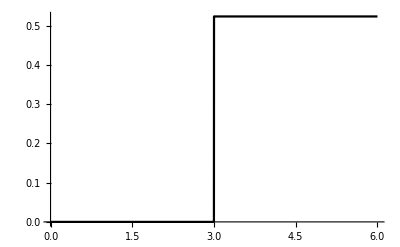

```mathematica
Le300=Plot[m7,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
THT=(Integrate[K6*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
Le301=Plot[TH,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All]
```

-Graphics-

## bottom

## convert to the model parameters

```mathematica
V0=Simplify[1/n1];
```

```mathematica
Vnmo1=V0*Sqrt[1+2*DELTA1];
```

```mathematica
Vnmo2=V0*Sqrt[1+2*DELTA2];
```

```mathematica
ETA1=(EPSLION1-DELTA1)/(1+2*DELTA1);
```

```mathematica
ETA2=(EPSLION2-DELTA2)/(1+2*DELTA2);
```

```mathematica
ETA3=Sqrt[(1+2*DELTA3)*(1+2*EPSLION1)*(1+2*ETA1)*(1+2*ETA2)/(1+2*EPSLION2)]-1;
```

## unsmoothed model parameters v0

```mathematica
vel0:=v01/;z<z0;
```

```mathematica
vel0:=v02/;z≥z0;
```

```mathematica
p10=Plot[vel0/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
p11=Plot[V0,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

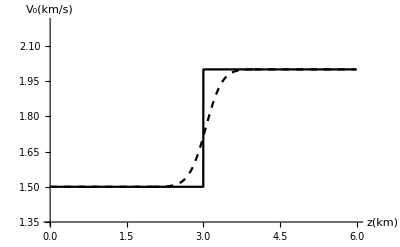

```mathematica
Show[{p10,p11},AxesOrigin->{0,1.35},PlotRange->{{0,6},{1.35,2.2}},AxesLabel->{Style["z(km)",FontSize->15],Style["V_0(km/s)",FontSize->15]}]
```

## unsmoothed model parameters v1

```mathematica
vel1:=v11/;z<z0;
```

```mathematica
vel1:=v12/;z≥z0;
```

```mathematica
p20=Plot[vel1/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

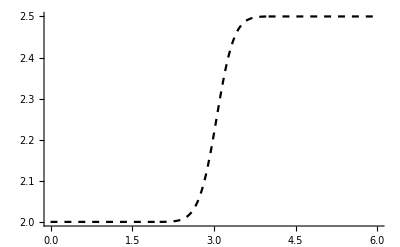

```mathematica
p21=Plot[Vnmo1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All]
```

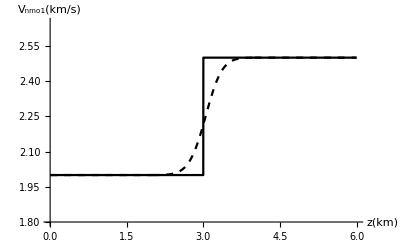

```mathematica
Show[{p20,p21},AxesOrigin->{0,1.8},PlotRange->{{0,6},{1.8,2.65}},AxesLabel->{Style["z(km)",FontSize->15],Style["V_nmo1(km/s)",FontSize->15]}]
```

## unsmoothed model parameters v2

```mathematica
vel2:=v21/;z<z0;
```

```mathematica
vel2:=v22/;z≥z0;
```

```mathematica
p30=Plot[vel2/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
p31=Plot[Vnmo2,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

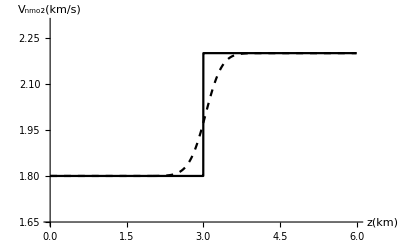

```mathematica
Show[{p30,p31},AxesOrigin->{0,1.65},PlotRange->{{0,6},{1.65,2.3}},AxesLabel->{Style["z(km)",FontSize->15],Style["V_nmo2(km/s)",FontSize->15]}]
```

## unsmoothed model parameters tht

```mathematica
t1:=th1/;z<z0;
```

```mathematica
t1:=th2/;z≥z0;
```

```mathematica
p40=Plot[t1/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All]
```

-Graphics-

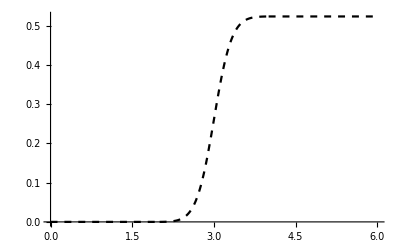

```mathematica
p41=Plot[THT,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All]
```

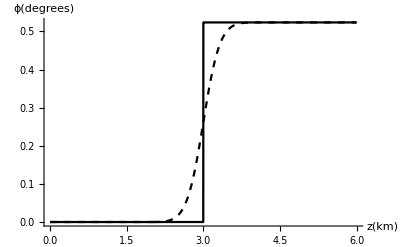

```mathematica
Show[{p40,p41},AxesOrigin->{0,-5},PlotRange->All,AxesLabel->{Style["z(km)",FontSize->15],Style["ϕ(degrees)",FontSize->15]}]
```

## part 3

## compare with unelipticall param

```mathematica
et1:=eta11/;z<z0;
```

```mathematica
et1:=eta12/;z≥z0;
```

```mathematica
p40a=Plot[et1/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
et2:=eta21/;z<z0;
```

```mathematica
et2:=eta22/;z≥z0;
```

```mathematica
p50=Plot[et2/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
p51=Plot[ETA2,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
et3:=eta31/;z<z0;
```

```mathematica
et3:=eta32/;z≥z0;
```

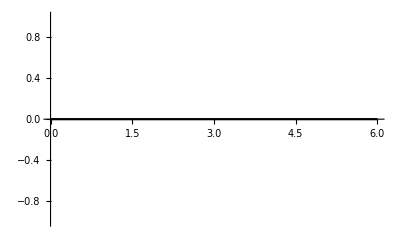

```mathematica
p60=Plot[et3/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
p61=Plot[ETA3,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

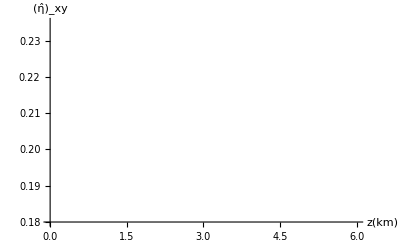

```mathematica
Show[{p60,p61},AxesOrigin->{0,0.18},PlotRange->{{0,6},{0.18,0.235}},AxesLabel->{Style["z(km)",FontSize->15],Style["(η̂)_xy",FontSize->15]}]
```

## unsmoothed traveltime

```mathematica
Xpp=Sum[(px vel1^2 (-1+(2 et2-et3) py^2 vel2^2)^2 *0.001)/(vel0 (1-2 et1 px^2 vel1^2-2 et2 py^2 vel2^2+(4 et1 et2-et3^2) px^2 py^2 vel1^2 vel2^2)^(3/2) √(1-(1+2 et1) px^2 vel1^2-(1+2 et2) py^2 vel2^2+((1+2 et1) (1+2 et2)-(1+et3)^2) px^2 py^2 vel1^2 vel2^2))/.px->(Cos[t1]*px0-Sin[t1]*py0)/.py->(Sin[t1]*px0+Cos[t1]*py0)/.param,{z,0,6,0.001}];
```

```mathematica
Ypp=Sum[(py (-1+(2 et1-et3) px^2 vel1^2)^2 vel2^2 *0.001)/(vel0 (1-2 et1 px^2 vel1^2-2 et2 py^2 vel2^2+(4 et1 et2-et3^2) px^2 py^2 vel1^2 vel2^2)^(3/2) √(1-(1+2 et1) px^2 vel1^2-(1+2 et2) py^2 vel2^2+((1+2 et1) (1+2 et2)-(1+et3)^2) px^2 py^2 vel1^2 vel2^2))/.px->(Cos[t1]*px0-Sin[t1]*py0)/.py->(Sin[t1]*px0+Cos[t1]*py0)/.param,{z,0,6,0.001}];
```

```mathematica
Tpp=Sum[((py^2 (-1+(2 et1-et3) px^2 vel1^2)^2 vel2^2+px^2 vel1^2 (-1+(2 et2-et3) py^2 vel2^2)^2+(1-2 et1 px^2 vel1^2-2 et2 py^2 vel2^2+(4 et1 et2-et3^2) px^2 py^2 vel1^2 vel2^2) (1-(1+2 et1) px^2 vel1^2-(1+2 et2) py^2 vel2^2+((1+2 et1) (1+2 et2)-(1+et3)^2) px^2 py^2 vel1^2 vel2^2)) *0.001)/(vel0 (1-2 et1 px^2 vel1^2-2 et2 py^2 vel2^2+(4 et1 et2-et3^2) px^2 py^2 vel1^2 vel2^2)^(3/2) √(1-(1+2 et1) px^2 vel1^2-(1+2 et2) py^2 vel2^2+((1+2 et1) (1+2 et2)-(1+et3)^2) px^2 py^2 vel1^2 vel2^2))/.px->(Cos[t1]*px0-Sin[t1]*py0)/.py->(Sin[t1]*px0+Cos[t1]*py0)/.param,{z,0,6,0.001}];
```

```mathematica
ParametricPlot3D[{Xpp,Ypp,Tpp},{px0,0,0.9},{py0,0,0.9},PlotRange->{{0,6},{0,6},{3.5,5.2}},AxesLabel->{Style["x(km)",FontSize->15],Style["y(km)",FontSize->15],Style["T_exact(s)",FontSize->15]},BoxRatios->{1, 1,0.5},RegionFunction->Function[{u,v,w},Abs[u]<7&&Abs[v]<7&&3.5<w<5.5],ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

## for the traveltime error

## traveltime error

#### For PTS

```mathematica
f11=1-(1+2*ETA1)*px^2*Vnmo1^2-(1+2*ETA2)*py^2*Vnmo2^2+((1+2*ETA1)*(1+2*ETA2)-(1+ETA3)^2)*px^2*py^2*Vnmo1^2*Vnmo2^2/.px->(Cos[THT]*px0-Sin[THT]*py0)/.py->(Sin[THT]*px0+Cos[THT]*py0);
```

```mathematica
f22=1-2*ETA1*px^2*Vnmo1^2-2*ETA2*py^2*Vnmo2^2+(4*ETA1*ETA2-ETA3^2)*px^2*py^2*Vnmo1^2*Vnmo2^2/.px->(Cos[THT]*px0-Sin[THT]*py0)/.py->(Sin[THT]*px0+Cos[THT]*py0);
```

```mathematica
Th11=((2*ETA1-ETA3)*px^2*Vnmo1^2-1)^2/.px->(Cos[THT]*px0-Sin[THT]*py0)/.py->(Sin[THT]*px0+Cos[THT]*py0);
```

```mathematica
Th22=((2*ETA2-ETA3)*py^2*Vnmo2^2-1)^2/.px->(Cos[THT]*px0-Sin[THT]*py0)/.py->(Sin[THT]*px0+Cos[THT]*py0);
```

```mathematica
Xppp=Sum[((px*Vnmo1^2*0.001*Th22)/(f22^(3/2)*f11^(1/2)*V0))/.px->(Cos[THT]*px0-Sin[THT]*py0)/.py->(Sin[THT]*px0+Cos[THT]*py0)/.param,{z,0,6,0.001}];
```

```mathematica
Yppp=Sum[(py*Vnmo2^2*0.001*Th11)/(f22^(3/2)*f11^(1/2)*V0)/.px->(Cos[THT]*px0-Sin[THT]*py0)/.py->(Sin[THT]*px0+Cos[THT]*py0)/.param,{z,0,6,0.001}];
```

```mathematica
Tppp=Sum[(0.001*(f11*f22+px^2*Vnmo1^2*Th22+py^2*Vnmo2^2*Th11))/(f22^(3/2)*f11^(1/2)*V0)/.px->(Cos[THT]*px0-Sin[THT]*py0)/.py->(Sin[THT]*px0+Cos[THT]*py0)/.param,{z,0,6,0.001}];
```

```mathematica
DT=Abs[Tpp-Tppp];
```

```mathematica
CRT=DT/.px0->0/.py0->0
```

0.0000833333

```mathematica
ParametricPlot3D[{Xpp/6,Ypp/6,Abs[DT-CRT]},{px0,0,0.9},{py0,0,0.9},PlotRange->{{0,1},{0,1},{0,0.025}},AxesLabel->{Style["x/z  ",FontSize->15],Style["y/z  ",FontSize->15],Style["|ΔT|(s)       ",FontSize->15]},BoxRatios->{1, 1,0.5},RegionFunction->Function[{u,v,w},Abs[u]<9&&Abs[v]<9&&0<w<0.04],ColorFunction->(ColorData["TemperatureMap",#3*10]&)]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Xpp/6,Ypp/6,Abs[DT-CRT]},{px0,0,0.9},{py0,0,0.9},PlotRange->{{0,1},{0,1},{0,0.02}},AxesLabel->{Style["x/z  ",FontSize->15],Style["y/z  ",FontSize->15],Style["|ΔT|(s)       ",FontSize->15]},BoxRatios->{1, 1,0.5},RegionFunction->Function[{u,v,w},Abs[u]<9&&Abs[v]<9&&0<w<0.04],ColorFunction->(ColorData["TemperatureMap",#3*10]&)]
```

-Graphics3D-